```mathematica
ClearAll["Global`*"]
SetDirectory["/Users/diegoandrade/Desktop/"];
Get[ "/Users/diegoandrade/Desktop/functions.m"]

(* Utilities *)
myPrint[args__,{style__}]:=Print[Row[{args},BaseStyle->{style}]];(* Utility to print info *)
```

```mathematica
(*Inteirior Points*)
imax = 2; (*Number of Cell in X direction *)
jmax = 2; (*Number of Cell in Y direction *)
xlength =1;
ylenght =1;
delx = 1/(imax);(* Spatial step interval in X direction *)
dely = 1/(jmax); (* Spatial step interval in Y direction *)
ustar=1; (* normalized velocity of lid *)
```

```mathematica
(* Time conditions *)
(* Initialize time value and time index *) 
timet=0;timen=0;(* timet:time value,timen:time index *)
delt = 0.02;  (*Time Step*)
tau = 0.5; (*Safety factor for time step size control τ*)
tend=100;
```

```mathematica
(*Pressure Itertion Data *)
it = 0;(* SOR counter  *)
res = 0;  (* Norm of pressure equation residual*)
eps = 0.001; (* Stopping tolerance for pressure iteration*)
gamma = 0.9;(*Upwind differencing factor γ*)
```

```mathematica
(*Problem Dependent quatities *)
(*Rey= 1000; (*Reynolds Number*)*)
Reynolds = List[1,10,100,1000,5000,10000];
GX = 0;(* Body forces *)
GY= 0;(* Body forces *)
UI = 0;  (* Initial Velocity *)
VI =0; (* Initial Velocity *)
PI = 0; (* Initial Pressure *)
Umed = 1; (*Mean velocity Value of the lid *)
itermax=100;(* Max iteration in SOR *)
omega=1.7;(* SOR Relaxation*)
TOL=0.001;(* SOR Tolerance*)
rindex=6;
```

```mathematica
(*Data Array Initialization *)
(*initialize and assign initial values to u,v,and p*)
U = Table[0,{imax+2},{jmax+2}];(* Velocity in x-direction *)
V = Table[0,{imax+2},{jmax+2}];(* Velocity in y-direction *)
P= Table[0,{imax+2},{jmax+2}] ;(* Pressure *)
wW=2;wE=2;wN=2;wS=2; (*flags to indicate no slip condition on a wall *)

(*Saving info*)
SU= Table[U,1*Round[tend]];
SV=Table[V,1*Round[tend]];

(*Saving Reynolds info info*)
RU= Table[U,Length[Reynolds]];
RV=Table[V,Length[Reynolds]];

(*F= Table[0,{imax+2},{jmax+2}]; (* F *)
G= Table[0,{imax+2},{jmax+2}]; (* G *)*)
GSV=Table[0,{(imax)*(jmax)}];(*Vector initialization for gauss seidel*)
```

```mathematica
(*Boundary Correction*)
(*U[[All,jmax+2 ]]=2*Umed-U[[All,jmax+1]] ;(*CORRECT THIS *)
U[[1,jmax+2]]=0.0; (*@ the wall *)
U[[imax+2,jmax+2]]=0.0; (* @ the wall *)*)
U=boundaryValuesU[U,ustar,imax,jmax,wN,wE,wW,wS];
V=boundaryValuesV[V,imax,jmax,wN,wE,wW,wS];
```

```mathematica
(* compute F and G according to Eqs.(3.36) and (3.37) *)
(* compute (d^2 u/d x^2) *)
d2ux = deriv2ux[U,imax,jmax,delx];
(* compute (d^2 u/d y^2) *)
d2uy = deriv2uy[U,imax,jmax,dely];
(* compute (d u^2/d x) *)
d1u2x=deriv1u2x[U,imax,jmax,delx, gamma];
(* compute (d uv/d y) *)
d1uvy=deriv1uvy[U,V,imax,jmax,dely,gamma];
(* compute (d^2 v/d x^2) *)
d2vx=deriv2vx[V,imax,jmax,delx];
(* compute (d^2 v/d y^2) *)
d2vy=deriv2vy[V,imax,jmax,dely];
(* compute (d v^2/d y) *)
d1v2y=deriv1v2y[V,imax,jmax,dely,gamma];
(* compute (d uv/d x) *)
d1uvx=deriv1uvx[U,V,imax,jmax,delx,gamma];
```

```mathematica
(* compute F and G *)
F=compF[U,imax,jmax,delx,delt,Reynolds[[rindex]],GX,d2ux,d2uy,d1u2x,d1uvy];
G= compG[V,imax,jmax,dely,delt,Reynolds[[rindex]],GY,d2vx,d2vy,d1uvx,d1v2y];
```

```mathematica
(* compute right-hand size of the pressure Eq.(3.38) *)
RHS=computeRHS[imax,jmax,delt,delx,dely,F,G];
```

```mathematica
(*Perform SOR*)
iter=0; (* index for iterative SOR *)
ritnorm=1;  (* tolerance (at first,it is set a large number) *)

While[ (iter<itermax && ritnorm>eps),
(* compute p of the next step, pNew *)
pNew = computepNew[imax,jmax,omega,delx,dely,P,RHS];
(* compute residual for pressure Eq.according to Eq.(3.45) *)
rit = computeRit[imax,jmax,delx,dely,P,RHS];
(* compute L^2 norm of residual according to Eq.(3.46) *)
   ritnorm=Norm[rit,Frobenius]/(imax*jmax);
(* update p *)
P=pNew;
(* increment counter *)
iter=iter+1;
]
```

```mathematica
(* compute u and v of the next step according to Eqs.(3.34) and (3.35) *)
```

```mathematica
U=computeU[U,imax,jmax,delt,delx,F,P];
V=computeV[V,imax,jmax,delt,dely,G,P].00;
timet=timet+delt;
timen=timen+1;
```

```mathematica
k=1; (*to save info after each time iteration*)
```

```mathematica
(* iterations after 1st iteration are written below *)
```

```mathematica
While[ timet < tend,
(*  select delta t according Eq.(3.50) after 1st time step *)
	delt=selectDelta[tau,Reynolds[[rindex]],delx,dely,U,V];
(* set boundary values for velocity u and v*)
	U=boundaryValuesU[U,ustar,imax,jmax,wN,wE,wW,wS];
	V=boundaryValuesV[V,imax,jmax,wN,wE,wW,wS];

(* compute F and G according to Eqs.(3.36) and (3.37) *)
(* compute (d^2 u/d x^2) *)
	d2ux = deriv2ux[U,imax,jmax,delx];
(* compute (d^2 u/d y^2) *)
	d2uy = deriv2uy[U,imax,jmax,dely];
(* compute (d u^2/d x) *)
	d1u2x=deriv1u2x[U,imax,jmax,delx, gamma];
(* compute (d uv/d y) *)
	d1uvy=deriv1uvy[U,V,imax,jmax,dely,gamma];
(* compute (d^2 v/d x^2) *)
	d2vx=deriv2vx[V,imax,jmax,delx];
(* compute (d^2 v/d y^2) *)
	d2vy=deriv2vy[V,imax,jmax,dely];
(* compute (d v^2/d y) *)
	d1v2y=deriv1v2y[V,imax,jmax,dely,gamma];
(* compute (d uv/d x) *)
	d1uvx=deriv1uvx[U,V,imax,jmax,delx,gamma];

(* set boundary values for pressure p,and F and G *)
P = boundaryValuesP[P,imax,jmax,wN,wE,wW,wS];
F=boundaryValuesF[U,imax,jmax,wN,wE,wW,wS];
G = boundaryValuesG[V,imax,jmax,wN,wE,wW,wS];

(* compute F and G *)
F=compF[U,imax,jmax,delx,delt,Reynolds[[rindex]],GX,d2ux,d2uy,d1u2x,d1uvy];
G= compG[V,imax,jmax,dely,delt,Reynolds[[rindex]],GY,d2vx,d2vy,d1uvx,d1v2y];

(* compute right-hand size of the pressure Eq.(3.38) *)
RHS=computeRHS[imax,jmax,delt,delx,dely,F,G];

(*Perform SOR*)
iter=0; (* index for iterative SOR *)
ritnorm=1;  (* tolerance (at first,it is set a large number) *)

While[ (iter<itermax && ritnorm>eps),
	(* compute p of the next step, pNew *)
	pNew = computepNew[imax,jmax,omega,delx,dely,P,RHS];
	(* compute residual for pressure Eq.according to Eq.(3.45) *)
	rit = computeRit[imax,jmax,delx,dely,P,RHS];
	(* compute L^2 norm of residual according to Eq.(3.46) *)
	        ritnorm=Norm[rit,Frobenius]/(imax*jmax);
	(* update p *)
	P=pNew;
	(* increment counter *)
	iter=iter+1;
	];

	U=computeU[U,imax,jmax,delt,delx,F,P];
	V=computeV[V,imax,jmax,delt,dely,G,P].00;
(* Prints Values after 10 iterations *)
	If[QuotientRemainder[timen,200][[2]]==0,Print["it# = " ,timen, " timet = ",timet ]];

(* For a videoclip saving info every second*)
If[(timet<k/1 && k/1≤timet+delt),
SU[[k]]=U;SV[[k]]=V;
(*Print[Style["Simulating at ",N[k/4], " seconds currently ..."];*)
myPrint["Simulating at ",N[k/1], " seconds currently ...",{FontSize->10,FontWeight->Bold,Background->LightGreen}];
k++;
];

(*	If[(timet<1.4&&1.4≤timet+delt),
		SU[[1]]=U;
		SV[[1]]=V;
,If[(timet<2.4&&2.4≤timet+delt),
		SU[[2]]=U;
		SV[[2]]=V;
,If[(timet<3.4&&3.4≤timet+delt),
		SU[[3]]=U;
		SV[[3]]=V;
,If[(timet<4.4&&4.4≤timet+delt),
		SU[[4]]=U;
		SV[[4]]=V;
,If[(timet<5.4&&5.4≤timet+delt),
		SU[[5]]=U;
		SV[[5]]=V;
,If[(timet<6.4&&6.4≤timet+delt),
		SU[[6]]=U;
		SV[[6]]=V;
,If[(timet<15.0&&15.0≤timet+delt),
		SU[[6]]=U;
		SV[[6]]=V;
,If[(timet<35.0&&35.0≤timet+delt),
		SU[[6]]=U;
		SV[[6]]=V;
]]]]]]]]; *)

(*increment counter*)
timet=timet+delt;
timen++;
];
```

Simulating at 1. seconds currently ...

Simulating at 2. seconds currently ...

Simulating at 3. seconds currently ...

Simulating at 4. seconds currently ...

Simulating at 5. seconds currently ...

Simulating at 6. seconds currently ...

Simulating at 7. seconds currently ...

Simulating at 8. seconds currently ...

Simulating at 9. seconds currently ...

Simulating at 10. seconds currently ...

Simulating at 11. seconds currently ...

Simulating at 12. seconds currently ...

Simulating at 13. seconds currently ...

Simulating at 14. seconds currently ...

Simulating at 15. seconds currently ...

Simulating at 16. seconds currently ...

Simulating at 17. seconds currently ...

Simulating at 18. seconds currently ...

Simulating at 19. seconds currently ...

Simulating at 20. seconds currently ...

Simulating at 21. seconds currently ...

Simulating at 22. seconds currently ...

Simulating at 23. seconds currently ...

Simulating at 24. seconds currently ...

it# = 200 timet = 24.895

Simulating at 25. seconds currently ...

Simulating at 26. seconds currently ...

Simulating at 27. seconds currently ...

Simulating at 28. seconds currently ...

Simulating at 29. seconds currently ...

Simulating at 30. seconds currently ...

Simulating at 31. seconds currently ...

Simulating at 32. seconds currently ...

Simulating at 33. seconds currently ...

Simulating at 34. seconds currently ...

Simulating at 35. seconds currently ...

Simulating at 36. seconds currently ...

Simulating at 37. seconds currently ...

Simulating at 38. seconds currently ...

Simulating at 39. seconds currently ...

Simulating at 40. seconds currently ...

Simulating at 41. seconds currently ...

Simulating at 42. seconds currently ...

Simulating at 43. seconds currently ...

Simulating at 44. seconds currently ...

Simulating at 45. seconds currently ...

Simulating at 46. seconds currently ...

Simulating at 47. seconds currently ...

Simulating at 48. seconds currently ...

Simulating at 49. seconds currently ...

it# = 400 timet = 49.895

Simulating at 50. seconds currently ...

Simulating at 51. seconds currently ...

Simulating at 52. seconds currently ...

Simulating at 53. seconds currently ...

Simulating at 54. seconds currently ...

Simulating at 55. seconds currently ...

Simulating at 56. seconds currently ...

Simulating at 57. seconds currently ...

Simulating at 58. seconds currently ...

Simulating at 59. seconds currently ...

Simulating at 60. seconds currently ...

Simulating at 61. seconds currently ...

Simulating at 62. seconds currently ...

Simulating at 63. seconds currently ...

Simulating at 64. seconds currently ...

Simulating at 65. seconds currently ...

Simulating at 66. seconds currently ...

Simulating at 67. seconds currently ...

Simulating at 68. seconds currently ...

Simulating at 69. seconds currently ...

Simulating at 70. seconds currently ...

Simulating at 71. seconds currently ...

Simulating at 72. seconds currently ...

Simulating at 73. seconds currently ...

Simulating at 74. seconds currently ...

it# = 600 timet = 74.895

Simulating at 75. seconds currently ...

Simulating at 76. seconds currently ...

Simulating at 77. seconds currently ...

Simulating at 78. seconds currently ...

Simulating at 79. seconds currently ...

Simulating at 80. seconds currently ...

Simulating at 81. seconds currently ...

Simulating at 82. seconds currently ...

Simulating at 83. seconds currently ...

Simulating at 84. seconds currently ...

Simulating at 85. seconds currently ...

Simulating at 86. seconds currently ...

Simulating at 87. seconds currently ...

Simulating at 88. seconds currently ...

Simulating at 89. seconds currently ...

Simulating at 90. seconds currently ...

Simulating at 91. seconds currently ...

Simulating at 92. seconds currently ...

Simulating at 93. seconds currently ...

Simulating at 94. seconds currently ...

Simulating at 95. seconds currently ...

Simulating at 96. seconds currently ...

Simulating at 97. seconds currently ...

Simulating at 98. seconds currently ...

Simulating at 99. seconds currently ...

it# = 800 timet = 99.895

Simulating at 100. seconds currently ...

```mathematica
MatrixForm[U]
MatrixForm[V]
```

(0 | 0. | 0. | 0
0.0129745 | -0.0130004 | 0.0130434 | 1.98707
0 | 0 | 0 | 2
0 | 0. | 0. | 0)

(0 | -0.0130465 | 0 | 0
0. | 0.0129272 | 0 | 0.
0. | -0.0129922 | 0 | 0.
0 | 0.0129826 | 0 | 0)

```mathematica
(*This function is used to plot the vector field creates a field that VectorFormUV can read ListVectorPlot*)
VectorFormUV[MatU_,MatV_,imax_,jmax_]:=
Module[{U=MatU,V=MatV,m=imax,n=jmax,S},
S=Table[{U[[i,j]],V[[i,j]]},{i,1,n+2},{j,1,m+2}];
Return[S];
];
```

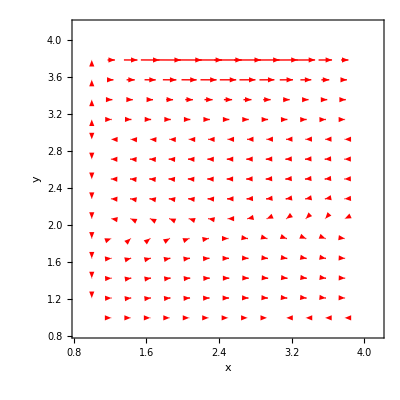

```mathematica
ListVectorPlot[VectorFormUV[U,V,imax,jmax],FrameLabel->{x,y},PerformanceGoal->"Speed",VectorStyle->Red]
```

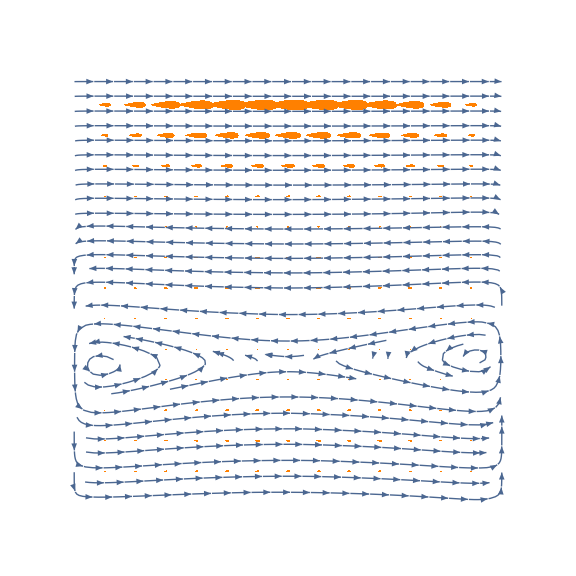

```mathematica
ListVectorPlot[VectorFormUV[SU[[40]],SV[[40]],imax,jmax],FrameLabel->{x,y},Frame->None,PerformanceGoal->"Quality",VectorStyle->{{Orange,"Drop"},{Green,"Dart"}},StreamPoints->45,StreamScale->Tiny,StreamScale->Tiny,AspectRatio->Automatic,PlotLegends->Automatic,ImageSize->Large]
```